```mathematica
Animate[Show[{ParametricPlot3D[{Cos[3*t]*(7-2*Cos[2*t]),Sin[3*t]*(7-2*Cos[2*t]),2*Sin[2*t]},{t,0,τ},PlotRange->{{-10,10},{-10,10},{-3,3}},PlotStyle->{Red,Thick},PlotPoints->100,MaxRecursion->10],ContourPlot3D[-(Sqrt[x^2+y^2]-7)^2-z^2+4==0,{x,-10,10},{y,-10,10},{z,-3,3},Mesh->None,ContourStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]]]}],{τ,0.1,10}]
```

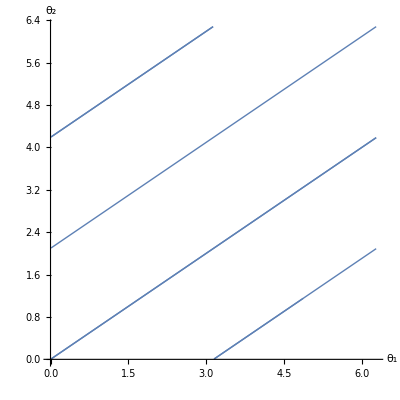

```mathematica
ParametricPlot[{Mod[3*t,2*Pi],Mod[2*t,2*Pi]},{t,0,10},PlotStyle->Thick,AspectRatio->1,AxesLabel->{Subscript[θ,1],Subscript[θ,2]}]
```

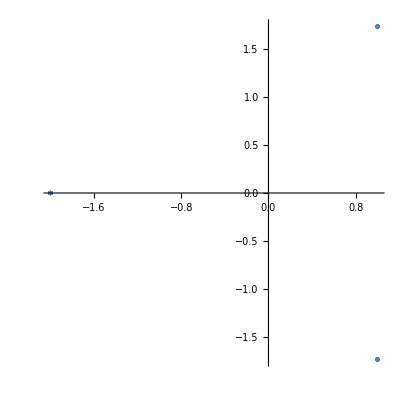

```mathematica
poincs2d=Table[{-2*Cos[2*2*Pi*n/3],2*Sin[2*2*Pi*n/3]},{n,0,100}];
ListPlot[poincs2d,PlotRange->All,PlotStyle->PointSize[Medium],AspectRatio->1]
```

```mathematica
Animate[Show[{ParametricPlot3D[{Cos[t/2]*(7-2*Cos[Pi*t]),Sin[t/2]*(7-2*Cos[Pi*t]),2*Sin[Pi*t]},{t,0,τ},PlotRange->{{-10,10},{-10,10},{-3,3}},PlotStyle->{Red,Thick},PlotPoints->100,MaxRecursion->10],ContourPlot3D[-(Sqrt[x^2+y^2]-7)^2-z^2+4==0,{x,-10,10},{y,-10,10},{z,-3,3},Mesh->None,ContourStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]]]}],{τ,0.1,100}]
```

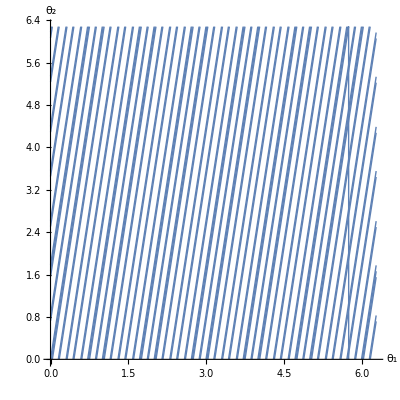

```mathematica
ParametricPlot[{Mod[t/2,2*Pi],Mod[Pi*t,2*Pi]},{t,0,200},PlotStyle->Thick,AspectRatio->1,AxesLabel->{Subscript[θ,1],Subscript[θ,2]},PlotPoints->100,MaxRecursion->10]
```

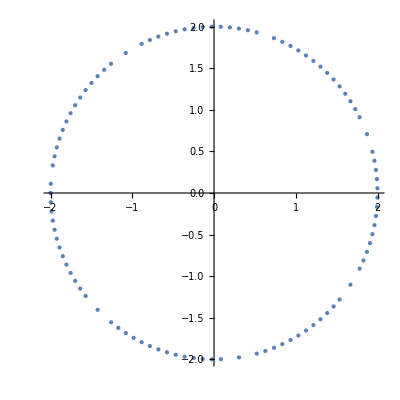

```mathematica
poincs2d=Table[{-2*Cos[Pi*4*Pi*n],2*Sin[Pi*4*Pi*n]},{n,0,100}];
ListPlot[poincs2d,PlotRange->All,PlotStyle->PointSize[Medium],AspectRatio->1]
```

```mathematica
ω1=5;
ω2=3;
k1=1;
k2=2;
```

```mathematica
sol1=NDSolve[{x1'[t]==ω1+k1*Sin[x2[t]-x1[t]],x2'[t]==ω2+k2*Sin[x1[t]-x2[t]],x1[0]==3,x2[0]==0},{x1,x2},{t,0,5}];
```

```mathematica
Animate[Show[{ParametricPlot3D[Evaluate[{Cos[x1[t]]*(7-2*Cos[x2[t]]),Sin[x1[t]]*(7-2*Cos[x2[t]]),2*Sin[x2[t]]}/.sol1],{t,0,τ},PlotRange->{{-10,10},{-10,10},{-3,3}},PlotStyle->{Red,Thick},PlotPoints->100,MaxRecursion->10],ContourPlot3D[-(Sqrt[x^2+y^2]-7)^2-z^2+4==0,{x,-10,10},{y,-10,10},{z,-3,3},Mesh->None,ContourStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]]]}],{τ,0.1,5}]
```

```mathematica
sollocked=ParallelTable[Evaluate[{Mod[x1[t],2*Pi],Mod[x2[t],2*Pi]}/.sol1][[1]],{t,0,5,0.001}];
```

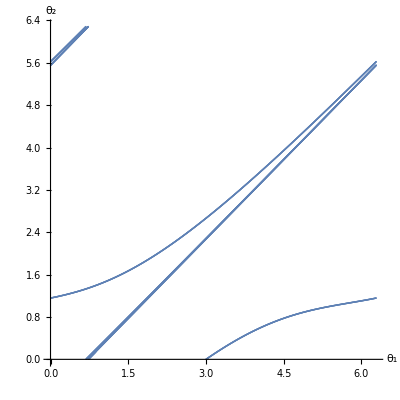

```mathematica
ListPlot[sollocked,AspectRatio->1,AxesLabel->{Subscript[θ,1],Subscript[θ,2]}]
```

```mathematica
ω1=5;
ω2=3;
k1=1;
k2=1/2;
```

```mathematica
sol2=NDSolve[{x1'[t]==ω1+k1*Sin[x2[t]-x1[t]],x2'[t]==ω2+k2*Sin[x1[t]-x2[t]],x1[0]==3,x2[0]==0},{x1,x2},{t,0,50}];
```

```mathematica
Animate[Show[{ParametricPlot3D[Evaluate[{Cos[x1[t]]*(7-2*Cos[x2[t]]),Sin[x1[t]]*(7-2*Cos[x2[t]]),2*Sin[x2[t]]}/.sol2],{t,0,τ},PlotRange->{{-10,10},{-10,10},{-3,3}},PlotStyle->{Red,Thick},PlotPoints->100,MaxRecursion->10],ContourPlot3D[-(Sqrt[x^2+y^2]-7)^2-z^2+4==0,{x,-10,10},{y,-10,10},{z,-3,3},Mesh->None,ContourStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]]]}],{τ,0.1,50}]
```

```mathematica
solnotlocked=ParallelTable[Evaluate[{Mod[x1[t],2*Pi],Mod[x2[t],2*Pi]}/.sol2][[1]],{t,0,50,0.001}];
```

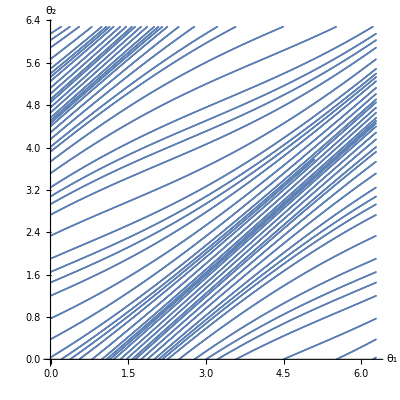

```mathematica
ListPlot[solnotlocked,AspectRatio->1,AxesLabel->{Subscript[θ,1],Subscript[θ,2]}]
```